```mathematica
v[r_,n_,l_]=Quantity["PlanckConstant"^2]l(l+1)/(4Pi^2 2 Quantity["ElectronMass"]r^2)-1/(4Pi Quantity["VacuumPermittivity"]) Quantity["ElementaryCharge"^2]/r
```

(l (1+l) (1/(8 π^2)))/r^2+(-1/(4 π))/r

```mathematica
v[r_,n_,l_]=Quantity["PlanckConstant"^2]l(l+1)/(4Pi^2 2 Quantity["ElectronMass"]r^2)-1/(4Pi Quantity["VacuumPermittivity"]) Quantity["ElementaryCharge"^2]/r
```

(l (1+l) (1/(8 π^2)))/r^2+(-1/(4 π))/r

```mathematica
Quantity["PlanckConstant"^2]/(4Pi^2)/Quantity["ElectronMass"]/Quantity["BohrRadius"^2]
```

1/(4 π^2)

```mathematica
UnitConvert[%]
```

4.35974×10^-18

```mathematica
vorfaktor=QuantityMagnitude[UnitConvert[%,Quantity["ElectronVolt"]]]
```

27.2114

```mathematica
v[rho_,l_]=vorfaktor(0.5 l(l+1)1/(rho^2)-1/rho)
```

27.2114 ((0.5 l (1+l))/rho^2-1/rho)

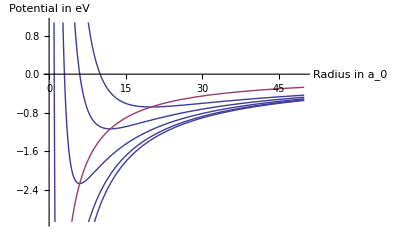

```mathematica
Plot[{Evaluate[Table[v[rho,n-1],{n,1,5}]],v[rho,-0.5+Sqrt[0.25+rho]]},{rho,0,50},AxesLabel->{"Radius in a_0", "Potential in eV"}]
```

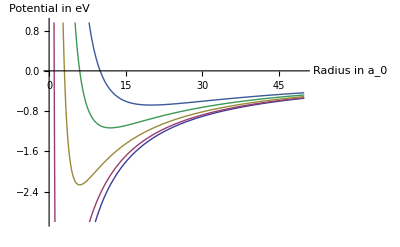

```mathematica
Plot[Evaluate[Table[v[rho,n-1],{n,1,5}]],{rho,0,50},AxesLabel->{"Radius in a_0", "Potential in eV"}]
```

## Teilaufgabe d

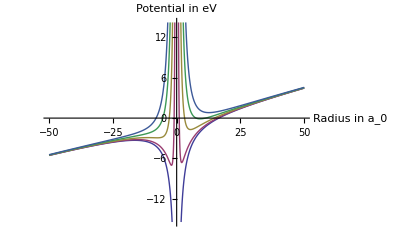

```mathematica
Plot[Evaluate[Table[v[Abs[rho],n-1]+rho/10,{n,1,5}]],{rho,-50,50},AxesLabel->{"Radius in a_0", "Potential in eV"}]
```

```mathematica
gradient[r_,l_,a0_,eryd_,efeld_,e_]:=eryd(-2l(l+1)a0^2+2a0 Abs[r])+efeld e r^3
```

```mathematica
gradient[1,2,1, 13.6, 1/10,1]
```

-135.9

```mathematica
Manipulate[Plot[Evaluate[Table[gradient[r,n-1,1, 13.6, efeld,1],{n,1,5}]],{r,-30,10},AxesLabel->{"Radius in a_0", "Indikatorfunktion"}],{efeld,0,1}]
```

```mathematica
s1=Solve[gradient[r,1,1,1,2,1]==0,r, Reals]
```

{{r→1}}

```mathematica
s1[[4]]
```

{r→(2 2^(1/3) a0 eryd)/((-54 a0^2 e^2 efeld^2 eryd l-54 a0^2 e^2 efeld^2 eryd l^2+√(864 a0^3 e^3 efeld^3 eryd^3+(-54 a0^2 e^2 efeld^2 eryd l-54 a0^2 e^2 efeld^2 eryd l^2)^2))^(1/3))-((-54 a0^2 e^2 efeld^2 eryd l-54 a0^2 e^2 efeld^2 eryd l^2+√(864 a0^3 e^3 efeld^3 eryd^3+(-54 a0^2 e^2 efeld^2 eryd l-54 a0^2 e^2 efeld^2 eryd l^2)^2))^(1/3))/(3 2^(1/3) e efeld)}